```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MonadicProgramming/MonadicLatentSemanticAnalysis.m"]
```

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MonadicProgramming/MonadicTracing.m"]
```

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/Misc/HeatmapPlot.m"]
```

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/Misc/RSparseMatrix.m"]
```

```mathematica
If[True,speeches=ResourceData[ResourceObject["Presidential Nomination Acceptance Speeches"]];
names=StringSplit[Normal[speeches[[All,"Person"]]][[All,2]],"::"][[All,1]],(*ELSE*)(*State of the union addresses provided by Christopher Wolfram.*)Get["~/MathFiles/Digital humanities/Presidential speeches/speeches.mx"];
names=Normal[speeches[[All,"Name"]]];];

dates=Normal[speeches[[All,"Date"]]];
texts=Normal[speeches[[All,"Text"]]];

Dimensions[speeches]
```

{51,8}

```mathematica
docWordRecords=Join@@MapThread[Thread[{##}]&,{Range@Length@texts,names,DateString[#,{"Year"}]&/@dates,DeleteStopwords@*TextWords/@ToLowerCase[texts]},1];
```

```mathematica
TableForm[RandomSample[docWordRecords,6],TableHeadings->{None,{"document index","name","year","word"}}]
```

document index | name | year | word
29 | WilliamHowardTaft | 1908 | reluctant
7 | HarrySTruman | 1948 | helps
38 | RichardMNixon | 1960 | khrushchev
39 | BarryGoldwater | 1964 | dedicated
41 | RichardMNixon | 1972 | 20
38 | RichardMNixon | 1960 | second

```mathematica
Multicolumn[RecordsSummary[docWordRecords,{"document index","name","year","word"},"MaxTallies"->8],4,Dividers->All,Alignment->Top]
```

The document-word matrix

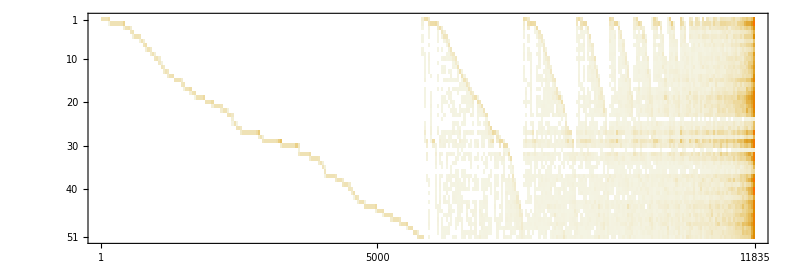

```mathematica
ctMat=CrossTabulate[docWordRecords[[All,{1,-1}]]];
MatrixPlot[Transpose@Sort@Map[#&,Transpose[ctMat@"XTABMatrix"]],MaxPlotPoints->300,ImageSize->800,AspectRatio->1/3]
```

The president-word matrix

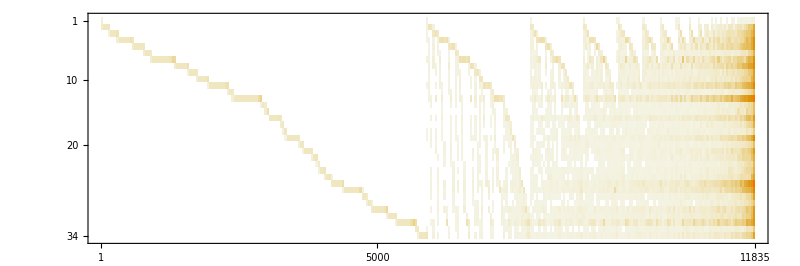

```mathematica
ctMat=CrossTabulate[docWordRecords[[All,{2,-1}]]];
MatrixPlot[Transpose@Sort@Map[#&,Transpose[ctMat@"XTABMatrix"]],MaxPlotPoints->300,ImageSize->800,AspectRatio->1/3]
```

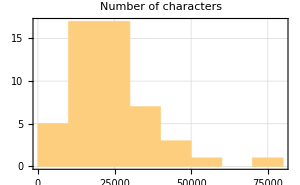
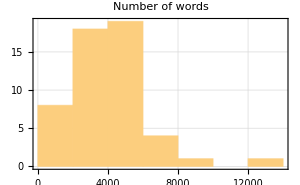
Pipeline value: Number of texts:51 | Number of unique words:19919
-Graphics- | -Graphics-

```mathematica
LSAMonUnit[texts]⟹LSAMonEchoTextCollectionStatistics[];
```

On way to obtain stop words:

```mathematica
stopWords=Complement[DictionaryLookup["*"],DeleteStopwords[DictionaryLookup["*"]]];
Length[stopWords]
RandomSample[stopWords,12]
```

347

{he'd,against,me,you'll,seemed,who's,IT,didn't,after,tit-for-tat,nor,you've}